```mathematica
Clear["Global`*"]
```

```mathematica
r = √(x^2+y^2);
```

```mathematica
F = ⅇ^-r/(1 + r^3);
```

```mathematica
g[x_]:= (ⅇ^(-x^2))/(1 +Abs[x]^2);
```

```mathematica
h[x_]:= ⅇ^(-Abs[x])/(1 +Abs[x]^3);
```

```mathematica
G = g[x]g[y]
H = h[x]h[y]
```

(ⅇ^(-x^2-y^2))/((1+Abs[x]^2) (1+Abs[y]^2))

ⅇ^(-Abs[x]-Abs[y])/((1+Abs[x]^3) (1+Abs[y]^3))

```mathematica
Plot3D[F,{x,-2,2},{y,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[G,{x,-2,2},{y,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[H,{x,-2,2},{y,-2,2},PlotRange->Full]
```

-Graphics3D-

```mathematica
y=x
```

x

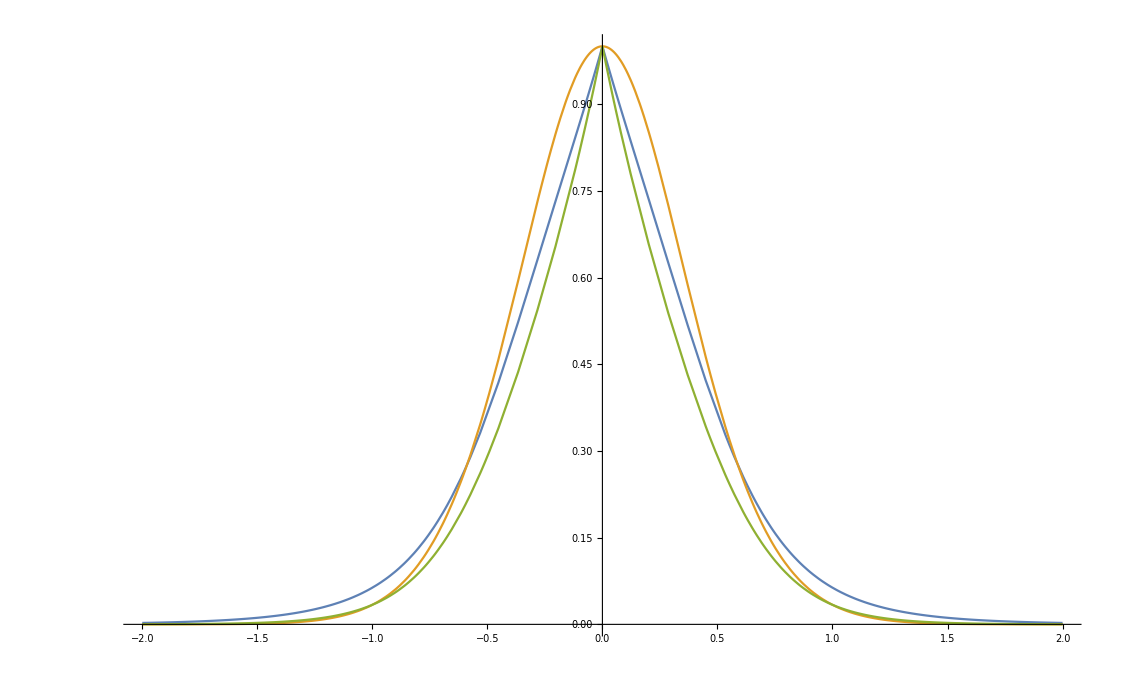

```mathematica
Plot[{F,G,H}  ,{x,-2,2}, PlotRange->Full]
```